```mathematica
ClearAll["Global`*"]
R5=R1;
R6=6R1;
R2=2R1;
R3=3R1;
R4=4R1;
ZL1=L1*s;
ZC1=1/(s*C1);
ZC1L1=Simplify[(ZC1*ZL1)/(ZC1+ZL1)];

Print["ZL1 = ", ZL1]
Print["ZC1 = ",ZC1]
Print["ZC1L1 = ",ZC1L1]
```

ZC1L1 = (L1 s)/(1+C1 L1 s^2)

ZC1 = 1/(C1 s)

ZL1 = L1 s

```mathematica
Za = (ZL1*ZC1)/(ZL1+ZC1);
```

```mathematica
e1 = V1(1/Za+1/R3+1/R2+1/R1)-V2(1/R1)-Uy(1/R2)==Ux/Za;
```

```mathematica
e2 = -V1(1/R1)+V2(1/R1+1/R4)-Uy(1/R4)==0;
```

```mathematica
e3 = -V1(1/R2)-V2(1/R4)+Uy(1/R4+1/R2)==0;
res = Solve[{e1,e2,e3}, {V1, V2, Uy}]
```

{{V1→(3 R1 (1+C1 L1 s^2) Ux)/(3 R1+L1 s+3 C1 L1 R1 s^2),V2→(3 R1 (1+C1 L1 s^2) Ux)/(3 R1+L1 s+3 C1 L1 R1 s^2),Uy→(3 R1 (1+C1 L1 s^2) Ux)/(3 R1+L1 s+3 C1 L1 R1 s^2)}}

```mathematica
V1 = res[[1,1,2]]
```

(3 R1 (1+C1 L1 s^2) Ux)/(3 R1+L1 s+3 C1 L1 R1 s^2)

```mathematica
V2 = res[[1,2,2]]
```

(3 R1 (1+C1 L1 s^2) Ux)/(3 R1+L1 s+3 C1 L1 R1 s^2)

```mathematica
Uy =res[[1,3,2]]
```

(3 R1 (1+C1 L1 s^2) Ux)/(3 R1+L1 s+3 C1 L1 R1 s^2)

```mathematica
UC = Collect[V1 + Ux, Ux]
```

(1+(3 R1 (1+C1 L1 s^2))/(3 R1+L1 s+3 C1 L1 R1 s^2)) Ux

```mathematica
IL= UC1/ZL1
```

((1+(3 R1 (1+C1 L1 s^2))/(3 R1+L1 s+3 C1 L1 R1 s^2)) Ux)/(L1 s)

```mathematica
(*тут решение узловыми*)
```

```mathematica
(*Дальше начинаются идентичные шаги*)

GL1=IL/Ux;
GC1=UC/Ux;
Gy=Uy/Ux;
Print["GL = ",Simplify[GL1]]
Print["GC = ",GC1]
Print["Gy = ",Gy]
```

GL = (1+(3 R1 (1+C1 L1 s^2))/(3 R1+L1 s+3 C1 L1 R1 s^2))/(L1 s)

GC = 1+(3 R1 (1+C1 L1 s^2))/(3 R1+L1 s+3 C1 L1 R1 s^2)

Gy = (3 R1 (1+C1 L1 s^2))/(3 R1+L1 s+3 C1 L1 R1 s^2)

```mathematica
(*Решаем уравнение в знаменетеле(Должен быть одинаковым
на токе, выходном напряжении и напряжении конденсатора)
```

```mathematica
sol=Solve[Denominator[Gy]==0,s]
p1=sol[[1,1,2]]/.R1->31/.L1->01.11*10^-3/.C1->7.131*10^-9;
p2=sol[[2,1,2]]/.R1->31/.L1->01.11*10^-3/.C1->7.131*10^-9;
p3=0;
Print["p1 = ",sol[[1,1,2]]," = ",p1]
Print["p2 = ",sol[[2,1,2]]," = ",p2]
Print["p3 = 0"]
```

{{s→-753940.-840487. ⅈ},{s→-753940.+840487. ⅈ}}

p1 = -753940.-840487. ⅈ = -753940.-840487. ⅈ

p2 = -753940.+840487. ⅈ = -753940.+840487. ⅈ

p3 = 0

```mathematica
(*Полюса приравниваем к решениям уравнения.
Третий полюс равен нулю*)
```

```mathematica
(*Сюда вставляется знаменатель умноженный на s*)
```

```mathematica
Dh[s_]:=Denominator[Gy]*s;
```

```mathematica
dDh[s_]:=Expand[D[Dh[s],s]];dDh[s]
(*Тут идут числители характеристик выходного напряжения, тока на индуктивности и напряжения на конденсаторе соответственно*)
```

3 R1+0.00022 s+7.05969×10^-12 R1 s^2

```mathematica
Ny[s_]=Numerator[Gy];
```

```mathematica
NL1[s_]=Numerator[GL1];
```

```mathematica
NC1[s_]=Numerator[GC1];
(*Дальше шаблонные вычисления*)
```

```mathematica
R1=31;
L1=0.11*10^-3;
C1=7.131*10^-9;
```

```mathematica
h1y=Ny[s]/dDh[s]/.s->p1;h2y=Ny[s]/dDh[s]/.s->p2;h3y=Ny[s]/dDh[s]/.s->p3;
h1C1=NC1[s]/dDh[s]/.s->p1;h2C1=NC1[s]/dDh[s]/.s->p2;h3C1=NC1[s]/dDh[s]/.s->p3;
h1L1=NL1[s]/dDh[s]/.s->p1;h2L1=NL1[s]/dDh[s]/.s->p2;h3L1=NL1[s]/dDh[s]/.s->p3;
Print[TemplateApply["h1y = ``, h2y = ``, h3y = ``",{h1y,h2y,h3y}]]
Print[TemplateApply["h1C1 = ``, h2C1 = ``, h3C1 = ``",ScientificForm/@{h1C1,h2C1,h3C1}]]
Print[TemplateApply["h1L = ``, h2L = ``, h3L = ``",{h1L1,h2L1,h3L1}]]
(*Ниже продолжение*)
```

h1y = 0.0000000000000000555112 - 0.897027i, h2y = 0.0000000000000000555112 + 0.897027i, h3y = 1.0

h1C1 = 0.0 - 84163569805085.i, h2C1 = 0.0 + 84163569805085.i, h3C1 = 0.0215054

h1L = 0.0 - 765123000000000000.i, h2L = 0.0 + 765123000000000000.i, h3L = 195.503

```mathematica
(*Также без изменений*)
```

```mathematica
hy=h1y*Exp[p1*t]+h2y*Exp[p2*t]+h3y*Exp[p3*t];
graphHC1=h1C1*Exp[p1*t]+h2C1*Exp[p2*t]+h3C1*Exp[p3*t];
```

```mathematica
graphHL1=h1L1*Exp[p1*t]+h2L1*Exp[p2*t]+h3L1*Exp[p3*t];
```

```mathematica
Print["hy(t) = ",ScientificForm[hy]]
Print["hC(t) = ",ScientificForm[graphHC1]]
Print["hL(t) = ",ScientificForm[graphHL1]]
```

hy(t) = 1.+(5.55112×10^-17-(8.97027×10^-1) ⅈ) ⅇ^((-7.5394×10^5-(8.40487×10^5) ⅈ) t)+(5.55112×10^-17+(8.97027×10^-1) ⅈ) ⅇ^((-7.5394×10^5+(8.40487×10^5) ⅈ) t)

hC(t) = 2.15054×10^-2-(0.+(8.41636×10^13) ⅈ) ⅇ^((-7.5394×10^5-(8.40487×10^5) ⅈ) t)+(0.+(8.41636×10^13) ⅈ) ⅇ^((-7.5394×10^5+(8.40487×10^5) ⅈ) t)

hL(t) = 2.15054×10^-2+(3.85209×10^-2-(1.26851×10^-2) ⅈ) ⅇ^((-6.23062×10^5-(8.67745×10^5) ⅈ) t)+(3.85209×10^-2+(1.26851×10^-2) ⅈ) ⅇ^((-6.23062×10^5+(8.67745×10^5) ⅈ) t)

```mathematica
(*Ваши значения из варианта*)
```

```mathematica
R1=27;L1=0.081/1000;C1=12.28/10^9;
(*PlotRange и GridLines могут отличаться от варианта к варианту.
Подбирайте экспериментально*)
```

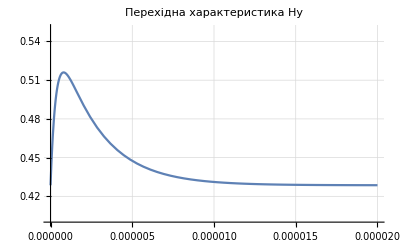

```mathematica
Plot[hy,{t,0,2*10^-5},PlotRange->{0.4,0.55},GridLines->Automatic,PlotLabel->HoldForm[Перехідна характеристика Hy]]
```

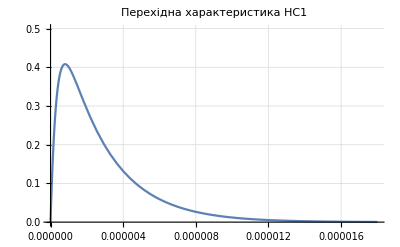

```mathematica
Plot[graphHC1,{t,0,1.8*10^-5},PlotRange->{0,0.5},GridLines->Automatic,PlotLabel->HoldForm[Перехідна характеристика HC1]]
```

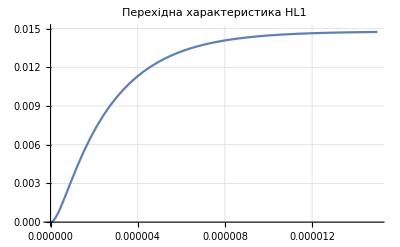

```mathematica
Plot[graphHL1,{t,0,1.5*10^-5},PlotRange->{0,0.015},GridLines->Automatic,PlotLabel->HoldForm[Перехідна характеристика HL1]]
```